```mathematica
Clear[r,c,s,rouAR,sig0,l1,l2,ss]; 
sig0 = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
l2[o_,r_] := E^(o √(1-1/r));
l1[o_,r_] := 1/l2[o,r];
ss[p1_,p2_,p3_,p4_] := -p1 Log[2,p1]-p2 Log[2,p2]-p3 Log[2,p3]-p4 Log[2,p4];

c[o_,r_]:= 1/(√(1+l1[o,r]));
s[o_,r_]:= √(1-c[o,r]^2);
rouAR[o_,r_] := 1/2({{c[o,r]^4, 0, 0, 0, 0, 0, c[o,r]^3, 0, 0, 0, 0, 0}, {0, s[o,r]^2 c[o,r]^2, 0, 0, 0, 0, 0, -s[o,r]^2 c[o,r], 0, 0, 0, 0}, {0, 0, s[o,r]^2 c[o,r]^2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, s[o,r]^4, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {c[o,r]^3, 0, 0, 0, 0, 0, c[o,r]^2, 0, 0, 0, 0, 0}, {0, -s[o,r]^2 c[o,r], 0, 0, 0, 0, 0, s[o,r]^2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}})
```

```mathematica
(*--------------------------------R----------------------------------*)
Clear[rouR,pR,sRouR,r];
rouR[o_,r_] = rouAR[o,r][[1;;4,1;;4]]+rouAR[o,r][[5;;8,5;;8]]+rouAR[o,r][[9;;12,9;;12]];
"Trace for R is : "
pR[o_,r_] = Simplify[Tr[rouR[o,r]]]
rouR[o_,r_] = Simplify[rouR[o,r]/pR[o,r]];
sRouR [o_,r_] = Simplify[ss[rouR[o,r][[1,1]],rouR[o,r][[2,2]],rouR[o,r][[3,3]],rouR[o,r][[4,4]]]]
"Entropy for R is : "
sRouR[50,1.00]
```

Trace for R is :

1

-(ⅇ^(2 o √((-1+r)/r)) Log[1/(2 (1+ⅇ^(-o √((-1+r)/r)))^2)]+ⅇ^(o √((-1+r)/r)) Log[ⅇ^(o √((-1+r)/r))/(2 (1+ⅇ^(o √((-1+r)/r)))^2)]+(2+ⅇ^(o √((-1+r)/r))) (Log[(2+ⅇ^(o √((-1+r)/r)))/(2 (1+ⅇ^(o √((-1+r)/r)))^2)]+ⅇ^(o √((-1+r)/r)) Log[(ⅇ^(o √((-1+r)/r)) (2+ⅇ^(o √((-1+r)/r))))/(2 (1+ⅇ^(o √((-1+r)/r)))^2)]))/(2 (1+ⅇ^(o √((-1+r)/r)))^2 Log[2])

Entropy for R is :

1.81128

```mathematica
(*--------------------------------X----------------------------------*)
```

```mathematica
(*---------------S(Subscript[ρ, 0]^x)-------------------*)
Clear[rouX0,pX0,sRouX0];
rouX0[o_,r_] := KroneckerProduct[({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}}),sig0].rouAR[o,r];
rouX0[o_,r_]= rouX0[o,r][[1;;4,1;;4]]+rouX0[o,r][[5;;8,5;;8]]+rouX0[o,r][[9;;12,9;;12]];
pX0[o_,r_] = Simplify[Tr[rouX0[o,r]]]
rouX0[o_,r_] = Simplify[rouX0[o,r]/pX0[o,r]];
sRouX0 [o_,r_] = Simplify[ss[rouX0[o,r][[1,1]],rouX0[o,r][[2,2]],rouX0[o,r][[3,3]],rouX0[o,r][[4,4]]]]
```

1/2

-(ⅇ^(2 o √((-1+r)/r)) Log[1/((1+ⅇ^(-o √((-1+r)/r)))^2)]+Log[1/((1+ⅇ^(o √((-1+r)/r)))^2)]+2 ⅇ^(o √((-1+r)/r)) Log[ⅇ^(o √((-1+r)/r))/((1+ⅇ^(o √((-1+r)/r)))^2)])/((1+ⅇ^(o √((-1+r)/r)))^2 Log[2])

```mathematica
(*---------------Subscript[ρ, 1]^x-------------------*)
```

```mathematica
Clear[rouX1,pX1,rouX1,sRouX1];
rouX1[o_,r_] := KroneckerProduct[1/2({{0, 0, 0}, {0, 1, 1}, {0, 1, 1}}),sig0].rouAR[o,r];
rouX1[o_,r_] = rouX1[o,r][[1;;4,1;;4]]+rouX1[o,r][[5;;8,5;;8]]+rouX1[o,r][[9;;12,9;;12]];
pX1[o_,r_] = Simplify[Tr[rouX1[o,r]]]
rouX1[o_,r_] = Simplify[rouX1[o,r]/pX1[o,r]]
sRouX1 [o_,r_] = ss[1,1,rouX1[o,r][[3,3]],rouX1[o,r][[4,4]]];
```

1/4

{{0,0,0,0},{0,0,0,0},{0,0,1/(1+ⅇ^(-o √((-1+r)/r))),0},{0,0,0,1/(1+ⅇ^(o √((-1+r)/r)))}}

```mathematica
(*---------------Subscript[ρ, 2]^x-------------------*)
```

```mathematica
Clear[rouX2,pX2,rouX2,sRouX2];
rouX2[o_,r_] := KroneckerProduct[1/2({{0, 0, 0}, {0, 1, -1}, {0, -1, 1}}),sig0].rouAR[o,r];
rouX2[o_,r_] = rouX2[o,r][[1;;4,1;;4]]+rouX2[o,r][[5;;8,5;;8]]+rouX2[o,r][[9;;12,9;;12]];
pX2[o_,r_] = Simplify[Tr[rouX2[o,r]]]
rouX2[o_,r_] = Simplify[rouX2[o,r]/pX2[o,r]]
sRouX2 [o_,r_] = ss[1,1,rouX2[o,r][[3,3]],rouX2[o,r][[4,4]]];

(*-------Subscript[S, x]------*)
Clear[sX];
sX[o_,r_] = Simplify[pX0[o,r] *sRouX0[o,r] + pX1[o,r] * sRouX1[o,r]+ pX2[o,r] * sRouX2[o,r]];
sX[50,1.00]
```

1/4

{{0,0,0,0},{0,0,0,0},{0,0,1/(1+ⅇ^(-o √((-1+r)/r))),0},{0,0,0,1/(1+ⅇ^(o √((-1+r)/r)))}}

1.5

```mathematica
(*--------------------------------Y----------------------------------*)
```

```mathematica
(*---------------Subscript[ρ, 0]^y-------------------*)
Clear[rouY0,pY0,rouY0,sRouY0];
rouY0[o_,r_] := KroneckerProduct[({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}}),sig0].rouAR[o,r];
rouY0[o_,r_] = rouY0[o,r][[1;;4,1;;4]]+rouY0[o,r][[5;;8,5;;8]]+rouY0[o,r][[9;;12,9;;12]];
pY0[o_,r_] = Simplify[Tr[rouY0[o,r]]]
rouY0[o_,r_] = Simplify[rouY0[o,r]/pY0[o,r]];
sRouY0 [o_,r_] = Simplify[ss[rouY0[o,r][[1,1]],rouY0[o,r][[2,2]],rouY0[o,r][[3,3]],rouY0[o,r][[4,4]]]]
```

1/2

-(ⅇ^(2 o √((-1+r)/r)) Log[1/((1+ⅇ^(-o √((-1+r)/r)))^2)]+Log[1/((1+ⅇ^(o √((-1+r)/r)))^2)]+2 ⅇ^(o √((-1+r)/r)) Log[ⅇ^(o √((-1+r)/r))/((1+ⅇ^(o √((-1+r)/r)))^2)])/((1+ⅇ^(o √((-1+r)/r)))^2 Log[2])

```mathematica
(*---------------Subscript[ρ, 1]^y-------------------*)
Clear[rouY1,pY1,rouY1,sRouY1];
rouY1[o_,r_] := KroneckerProduct[1/2({{0, 0, 0}, {0, 1, -I}, {0, I, 1}}),sig0].rouAR[o,r];
rouY1[o_,r_] = rouY1[o,r][[1;;4,1;;4]]+rouY1[o,r][[5;;8,5;;8]]+rouY1[o,r][[9;;12,9;;12]];
pY1[o_,r_] = Simplify[Tr[rouY1[o,r]]]
rouY1[o_,r_] = Simplify[rouY1[o,r]/pY1[o,r]]
sRouY1 [o_,r_] = ss[1,1,rouY1[o,r][[3,3]],rouY1[o,r][[4,4]]];
```

1/4

{{0,0,0,0},{0,0,0,0},{0,0,1/(1+ⅇ^(-o √((-1+r)/r))),0},{0,0,0,1/(1+ⅇ^(o √((-1+r)/r)))}}

```mathematica
(*---------------Subscript[ρ, 2]^y-------------------*)
Clear[rouY2,pY2,rouY2,sRouY2];
rouY2[o_,r_] := KroneckerProduct[1/2({{0, 0, 0}, {0, 1, I}, {0, -I, 1}}),sig0].rouAR[o,r];
rouY2[o_,r_] = rouY2[o,r][[1;;4,1;;4]]+rouY2[o,r][[5;;8,5;;8]]+rouY2[o,r][[9;;12,9;;12]];
pY2[o_,r_] = Simplify[Tr[rouY2[o,r]]]
rouY2[o_,r_] = Simplify[rouY2[o,r]/pY2[o,r]]
sRouY2 [o_,r_] = ss[1,1,rouY2[o,r][[3,3]],rouY2[o,r][[4,4]]];
```

1/4

{{0,0,0,0},{0,0,0,0},{0,0,1/(1+ⅇ^(-o √((-1+r)/r))),0},{0,0,0,1/(1+ⅇ^(o √((-1+r)/r)))}}

```mathematica
(*-------Subscript[S, y]------*)
Clear[sY,r];
sY[o_,r_] = Simplify[pY0[o,r] *sRouY0[o,r] + pY1[o,r] * sRouY1[o,r]+ pY2[o,r] * sRouY2[o,r]];
sY[50,1.00]
```

1.5

```mathematica
(*--------------------------------Z----------------------------------*)
```

```mathematica
(*---------------Subscript[ρ, 0]^z-------------------*)
Clear[rouZ0,pZ0,rouZ0,sRouZ0];
rouZ0[o_,r_] := KroneckerProduct[({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}}),sig0].rouAR[o,r];
rouZ0[o_,r_] = rouZ0[o,r][[1;;4,1;;4]]+rouZ0[o,r][[5;;8,5;;8]]+rouZ0[o,r][[9;;12,9;;12]];
pZ0[o_,r_] = Simplify[Tr[rouZ0[o,r]]]
rouZ0[o_,r_] = Simplify[rouZ0[o,r]/pZ0[o,r]];
sRouZ0 [o_,r_] = Simplify[ss[rouZ0[o,r][[1,1]],rouZ0[o,r][[2,2]],rouZ0[o,r][[3,3]],rouZ0[o,r][[4,4]]]]
```

1/2

-(ⅇ^(2 o √((-1+r)/r)) Log[1/((1+ⅇ^(-o √((-1+r)/r)))^2)]+Log[1/((1+ⅇ^(o √((-1+r)/r)))^2)]+2 ⅇ^(o √((-1+r)/r)) Log[ⅇ^(o √((-1+r)/r))/((1+ⅇ^(o √((-1+r)/r)))^2)])/((1+ⅇ^(o √((-1+r)/r)))^2 Log[2])

```mathematica
(*---------------Subscript[ρ, 1]^z-------------------*)
Clear[rouZ1,pZ1,rouZ1,sRouZ1];
rouZ1[o_,r_] := KroneckerProduct[({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}),sig0].rouAR[o,r];
rouZ1[o_,r_] = rouZ1[o,r][[1;;4,1;;4]]+rouZ1[o,r][[5;;8,5;;8]]+rouZ1[o,r][[9;;12,9;;12]];
pZ1[o_,r_] = Simplify[Tr[rouZ1[o,r]]]
rouZ1[o_,r_] = Simplify[rouZ1[o,r]/pZ1[o,r]]
sRouZ1 [o_,r_] = ss[1,1,rouZ1[o,r][[3,3]],rouZ1[o,r][[4,4]]];
```

1/2

{{0,0,0,0},{0,0,0,0},{0,0,1/(1+ⅇ^(-o √((-1+r)/r))),0},{0,0,0,1/(1+ⅇ^(o √((-1+r)/r)))}}

```mathematica
(*---------------Subscript[ρ, 2]^Z-------------------*)
Clear[rouZ2,pZ2,rouZ2,sRouZ2];
rouZ2[o_,r_] := KroneckerProduct[({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}),sig0].rouAR[o,r];
rouZ2[o_,r_] = rouZ2[o,r][[1;;4,1;;4]]+rouZ2[o,r][[5;;8,5;;8]]+rouZ2[o,r][[9;;12,9;;12]];
pZ2[o_,r_] = Simplify[Tr[rouZ2[o,r]]]
(*rouZ2[o_,r_] = Simplify[rouZ2[o,r]/pZ2[o,r]] 
sRouZ2[o_,r_] = ss[rouZ2[o,r][[1,1]],rouZ2[o,r][[2,2]],rouX2[o,r][[3,3]],rouX2[o,r][[4,4]]];*)
```

0

```mathematica
(*-------Subscript[S, z]------*)
Clear[sZ];
sZ[o_,r_] = Simplify[ pZ0[o,r] *sRouZ0[o,r] +pZ1[o,r] * sRouZ1[o,r]];
sZ[50,1.00]
```

1.5

```mathematica
(*----------------------------Graph---------------------------------*)
```

1.37744

0.947771

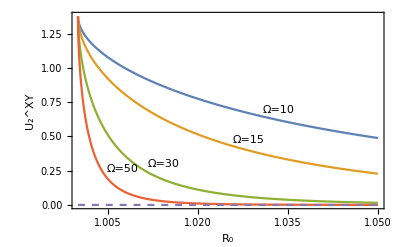

```mathematica
(*----------------Subscript[R, 2]^xy-----------------*)
Clear[q2XY,g1,o,r];
q2XY[o_,r_] = Simplify[-2 *sRouR[o,r] + sX[o,r] + sY[o,r]];
q2XY[50,1.00]+2
q2XY[10,1.01] +2
g1 = Plot[{q2XY[10,r]+2,q2XY[15,r]+2,q2XY[30,r]+2,q2XY[50,r]+2,0}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_2^XY"},PlotStyle->{{},{},{},{},{Dashed}},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

1.37744

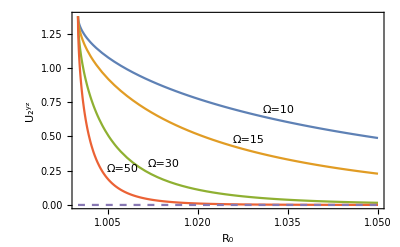

```mathematica
(*----------------Subscript[R, 2]^yz-----------------*)
Clear[q2YZ,g2];
q2YZ[o_,r_] = Simplify[-2 *sRouR[o,r] + sY[o,r] + sZ[o,r]];
q2YZ[50,1.00]+2
g2 = Plot[{q2YZ[10,r]+2,q2YZ[15,r]+2,q2YZ[30,r]+2,q2YZ[50,r]+2,0}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_2^yz"},PlotStyle->{{},{},{},{},{Dashed}},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

1.37744

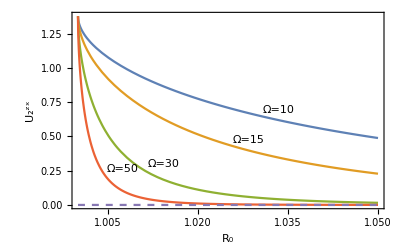

```mathematica
(*----------------Subscript[R, 2]^zx-----------------*)
Clear[q2ZX,g3];
q2ZX[o_,r_] = Simplify[-2 *sRouR[o,r] + sZ[o,r] + sX[o,r]];
q2ZX[50,1.00]+2
g3 = Plot[{q2ZX[10,r]+2,q2ZX[15,r]+2,q2ZX[30,r]+2,q2ZX[50,r]+2,0}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_2^zx"},RotateLabel->False,PlotStyle->{{},{},{},{},{Dashed}},PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

1.37744

0.947771

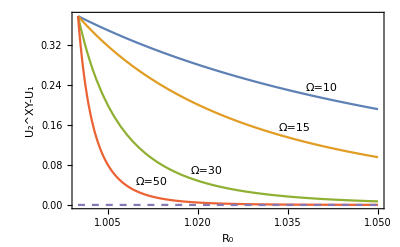

```mathematica
(*------------------------Subscript[Q, 2]-Subscript[Q, 1]-------------------------*)
sigI = {{1,0},{0,1}};
sig1 = {{0,1},{1,0}} ;
sig2 = {{0,-I},{I,0}};
sig3 = {{1,0},{0,-1}};

part1 = c3* Outer[Times, sig3, sig3] ;
part2 = Outer[Times, sigI, {{1,0},{0,0}}];
part3 = (3+l2[o,r] + 2*l1[o,r])/(1 + l2[o,r]) * Outer[Times, sigI, {{0,0},{0,1}}];
part4 = c1 * Sqrt[1+l1[o,r]] * Outer[Times, sig1, sig1];
part5 = c2 *  Sqrt[1+l1[o,r]] * Outer[Times, sig2, sig2] ; 
rouAI = 1/4/(1+ l1[o,r]) * (part1 + part2 + part3 + part4 + part5) ;
rouAI = Flatten[rouAI,{{1,3},{2,4}}] ;

hbin[p_] = -p Log[2,p] - (1-p) Log[2,(1-p)];
nl2 [o_,r_]= 1/(2 + 2 l2[o,r]);
nnl2[o_,r_] = l2[o,r]/(2+2 l2[o,r]);
u1 = Composition[hbin,nl2];
u2 = Composition[hbin,nnl2];

Clear[q2XY,g1,o,r];
q2XY[o_,r_] = Simplify[-2 *sRouR[o,r] + sX[o,r] + sY[o,r]];
q2XY[50,1.00]+2
q2XY[10,1.01] +2
g1 = Plot[{q2XY[10,r]+2-(1+u1[10,r]-u2[10,r]),q2XY[15,r]+2-(1+u1[15,r]-u2[15,r]),q2XY[30,r]+2-(1+u1[30,r]-u2[30,r]),q2XY[50,r]+2-(1+u1[50,r]-u2[50,r]),0}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_2^XY-U_1"},PlotStyle->{{},{},{},{},{Dashed}},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

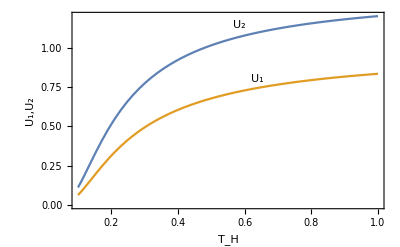

```mathematica
(*----------------------------Subscript[T, H](1.02)-------------------------*)
Clear[r00];
r00 = 1.02;
Plot[{q2XY[3/t,r00]+2, 1+u1[3/t,r00]-u2[3/t,r00]},{t,0.1,1},Frame->True,FrameLabel->{{"U_1,U_2",""},{"T_H","R_0=1.02"}},RotateLabel->False,PlotLabels->Placed[{"U_2","U_1"},{Scaled[0.65],Above}]]
```

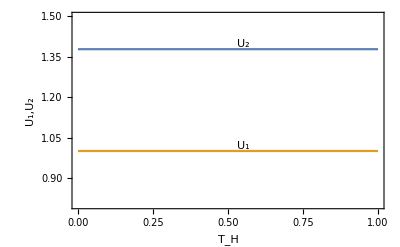

```mathematica
r00 = 1;
Plot[{q2XY[3/t,r00]+2, 1+u1[3/t,r00]-u2[3/t,r00]},{t,0,1},Frame->True,FrameLabel->{{"U_1,U_2",""},{"T_H","R_0=1"}},RotateLabel->False,PlotRange->{0.8,1.5},PlotLabels->Placed[{"U_2","U_1"},{Scaled[0.55],Above}]]
```

```mathematica
(*----------------------Width-------------------------*)
```

```mathematica
Clear[rouAB,rouA,rouB,eigRouAB,x];o=50;r=1.00;c[o_,r_]:= 1/(√(1+l1[o,r]));s[o_,r_]:= √(1-c[o,r]^2);Clear[o,r];Clear[c,s];
c[o_,r_]=√x;s[o_,r_]:= √(1-c[o,r]^2);
rouAB[o_,r_]= 1/2({{c[o,r]^4, 0, 0, 0, 0, 0, c[o,r]^3 s[o,r], 0, 0, c[o,r]^3 s[o,r], 0, 0, 0, 0, 0, c[o,r]^2 s[o,r]^2}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {c[o,r]^3 s[o,r], 0, 0, 0, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, 0, 0, 0, c[o,r] s[o,r]^3}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, c[o,r]^2, 0, 0, 0, 0, 0, -c[o,r]s[o,r], 0}, {c[o,r]^3 s[o,r], 0, 0, 0, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, 0, 0, 0, c[o,r] s[o,r]^3}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -c[o,r]s[o,r], 0, 0, 0, 0, 0, s[o,r]^2, 0}, {c[o,r]^2 s[o,r]^2, 0, 0, 0, 0, 0, c[o,r] s[o,r]^3, 0, 0, c[o,r] s[o,r]^3, 0, 0, 0, 0, 0, s[o,r]^4}});
eigRouAB[o_,r_] = Simplify[Eigenvalues[rouAB[o,r]]] ;
rouB[o_,r_] = Simplify[rouAB[o,r][[1;;4,1;;4]]+rouAB[o,r][[5;;8,5;;8]]+rouAB[o,r][[9;;12,9;;12]]+rouAB[o,r][[13;;16,13;;16]]]  // MatrixForm
rouA[o_,r_] = Simplify[Map[Tr,Partition[rouAB[o,r],{4,4}] ,{2}]] // MatrixForm
```

(1/2 x (1+x) | 0 | 0 | 0
0 | -1/2 (-1+x) x | 0 | 0
0 | 0 | 1/2 (1-x^2) | 0
0 | 0 | 0 | 1/2 (-1+x)^2)

(x^2/2 | 0 | 0 | 0
0 | -1/2 (-1+x) x | 0 | 0
0 | 0 | -1/2 (-2+x) x | 0
0 | 0 | 0 | 1/2 (2-3 x+x^2))

```mathematica
lo[p_] := -p Log[2,p];
(*NSolve[lo[x]==1/3,x]*)
```

3.62256

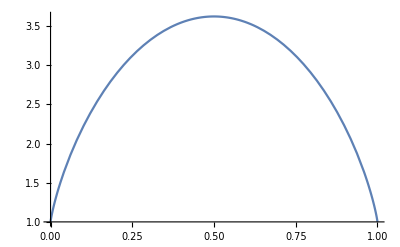

{x→0.928187}

```mathematica
Clear[ab];
ab[x_]:=lo[1/2 x (1+x)]+lo[-1/2 (-1+x) x]+lo[1/2 (1-x^2)]+lo[1/2 (-1+x)^2]+lo[x^2/2]+lo[-1/2 (-1+x) x]+lo[-1/2 (-2+x) x]+lo[1/2 (2-3 x+x^2)]
ab[0.5]
Plot[ab[x],{x,0,1}]
FindRoot[ab[x] == (4 (lo[1/8]+lo[3/8])-1)/E+1,{x,0.9718}]
```

```mathematica
Clear[rouAB1,rouA1,rouB1];o=50;r=1.00;Clear[o,r];Clear[c,s];s[o_,r_]:= √(1-c[o,r]^2);
rouAB1[o_,r_]= 1/2({{c[o,r]^4, 0, 0, 0, 0, 0, c[o,r]^3 s[o,r], 0, 0, c[o,r]^3 s[o,r], 0, 0, 0, 0, 0, c[o,r]^2 s[o,r]^2}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, c[o,r]^2, 0, 0, 0, 0, 0, 0, 0, 0, -c[o,r]s[o,r], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {c[o,r]^3 s[o,r], 0, 0, 0, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, 0, 0, 0, c[o,r] s[o,r]^3}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {c[o,r]^3 s[o,r], 0, 0, 0, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, 0, 0, 0, c[o,r] s[o,r]^3}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -c[o,r]s[o,r], 0, 0, 0, 0, 0, 0, 0, 0, s[o,r]^2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {c[o,r]^2 s[o,r]^2, 0, 0, 0, 0, 0, c[o,r] s[o,r]^3, 0, 0, c[o,r] s[o,r]^3, 0, 0, 0, 0, 0, s[o,r]^4}});
rigRouAB1[o_,r_] = Simplify[Eigenvalues[rouAB1[o,r]]] 
rouB1[o_,r_] = Simplify[rouAB1[o,r][[1;;4,1;;4]]+rouAB1[o,r][[5;;8,5;;8]]+rouAB1[o,r][[9;;12,9;;12]]+rouAB1[o,r][[13;;16,13;;16]]]  // MatrixForm
rouA1[o_,r_] = Simplify[Map[Tr,Partition[rouAB1[o,r],{4,4}] ,{2}]] // MatrixForm
```

{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

(1/2 (c[o,r]^2+c[o,r]^4) | 0 | 0 | 0
0 | 1/2 (1-c[o,r]^4) | 0 | 0
0 | 0 | -1/2 c[o,r]^2 (-1+c[o,r]^2) | 0
0 | 0 | 0 | 1/2 (-1+c[o,r]^2)^2)

(1/2 c[o,r]^4 | 0 | 0 | 0
0 | c[o,r]^2-1/2 c[o,r]^4 | 0 | 0
0 | 0 | -1/2 c[o,r]^2 (-1+c[o,r]^2) | 0
0 | 0 | 0 | 1/2 (2-3 c[o,r]^2+c[o,r]^4))